FittedModel[-0.0000105591+0.468428 x]

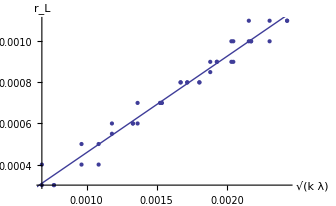

```mathematica
(*Aufgabe 1.1*)
radius[r1_]:=Abs[r1-20.5]*10^-3;
lambdag=59*10^-8;
lambdab=465*10^-9;

werte={{Sqrt[1*lambdag],radius[20.2]},{Sqrt[2*lambdag],radius[20.1]},{Sqrt[3*lambdag],radius[19.9]},{Sqrt[4*lambdag],radius[19.8]},{Sqrt[5*lambdag],radius[19.7]},{Sqrt[6*lambdag],radius[19.65]},{Sqrt[7*lambdag],radius[19.5]},{Sqrt[8*lambdag],radius[19.5]},{Sqrt[9*lambdag],radius[19.4]},{Sqrt[10*lambdag],radius[19.4]},{Sqrt[1*lambdag],radius[20.8]},{Sqrt[2*lambdag],radius[21]},{Sqrt[3*lambdag],radius[21.1]},{Sqrt[4*lambdag],radius[21.2]},{Sqrt[5*lambdag],radius[21.3]},{Sqrt[6*lambdag],radius[21.4]},{Sqrt[7*lambdag],radius[21.4]},{Sqrt[8*lambdag],radius[21.5]},{Sqrt[9*lambdag],radius[21.5]},{Sqrt[10*lambdag],radius[21.6]},{Sqrt[1*lambdab],radius[20.2]},{Sqrt[2*lambdab],radius[20.1]},{Sqrt[3*lambdab],radius[19.9]},{Sqrt[4*lambdab],radius[19.8]},{Sqrt[5*lambdab],radius[19.8]},{Sqrt[6*lambdab],radius[19.7]},{Sqrt[7*lambdab],radius[19.7]},{Sqrt[8*lambdab],radius[19.6]},{Sqrt[9*lambdab],radius[19.5]},{Sqrt[10*lambdab],radius[19.4]},
{Sqrt[1*lambdab],radius[20.9]},{Sqrt[2*lambdab],radius[21]},{Sqrt[3*lambdab],radius[21.05]},{Sqrt[4*lambdab],radius[21.1]},{Sqrt[5*lambdab],radius[21.2]},{Sqrt[6*lambdab],radius[21.3]},{Sqrt[7*lambdab],radius[21.3]},{Sqrt[8*lambdab],radius[21.4]},{Sqrt[9*lambdab],radius[21.4]},{Sqrt[10*lambdab],radius[21.5]}};

model=LinearModelFit[werte,x,x]
Show[ListPlot[werte],Plot[model["BestFit"],{x,0,1}],AxesLabel->{Sqrt[k*λ], Subscript[r, L] }]
```

```mathematica
FittedModel[-0.000010559050463607575+0.46842844833139496 x]
```

FittedModel[4.07808×10^-9+1.06684 x]

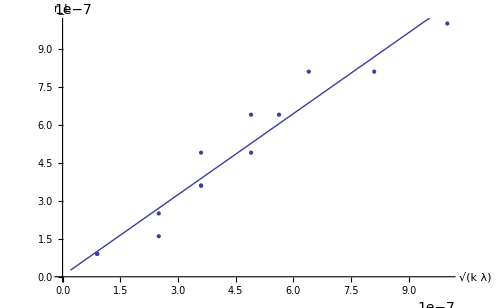

```mathematica
radiusW[r1_]:=(Abs[r1-19.4]*10^-3)^2;
werte1={{radiusW[19.1],(radius[20.2])^2},{radiusW[18.9],(radius[20.1])^2},{radiusW[18.8],(radius[19.9])^2},{radiusW[18.7],(radius[19.8])^2},{radiusW[18.65],(radius[19.7])^2},{radiusW[19.7],(radius[20.8])^2},{radiusW[19.9],(radius[21])^2},{radiusW[20],(radius[21.1])^2},{radiusW[20],(radius[21.2])^2},{radiusW[20.1],(radius[21.3])^2},{radiusW[20.2],(radius[21.4])^2},{radiusW[20.3],(radius[21.4])^2},{radiusW[20.4],(radius[21.5])^2}};
model1=LinearModelFit[werte1,x,x]
Show[ListPlot[werte1],Plot[model1["BestFit"],{x,0,1}],AxesLabel->{Sqrt[k*λ], Subscript[r, L] }]
```